# Relativity of Simultaneity

## In 1D

### Speed of light

```mathematica
c=299792458;
```

### Relative velocity between inertial reference frames

```mathematica
v=0.8c;
```

### Ratio of relative velocity v to the speed of light c

```mathematica
β[𝓋_]=𝓋/c;
```

```mathematica
β[v]
```

0.8

### Lorentz factor

```mathematica
γ[𝓋_]=1/(√(1-β[𝓋]^2));
```

```mathematica
γ[v]
```

1.66667

### Simultaneity

```mathematica
t':=10
```

```mathematica
t[𝓋_,x.b4_]=γ[𝓋](t'+(𝓋/c^2)x.b4);
```

```mathematica
t[v,0]
```

16.6667

```mathematica
t[v,c]
```

18.

```mathematica
t[v,2c]
```

19.3333

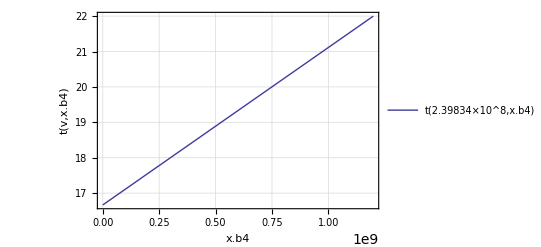

```mathematica
Plot[t[v,x.b4],{x.b4,0,4c},AxesLabel->{"x.b4","t(v,x.b4)"},PlotLegends->"Expressions",Frame-> True,GridLines->Automatic]
```